```mathematica
Exit[]
```

## Initial condition

```mathematica
Get[NotebookDirectory[]<>"eoms.wl"];
Needs["DifferentialEquations`NDSolveProblems`"];
Needs["DifferentialEquations`NDSolveUtilities`"];
```

```mathematica
bdy0={Ex[x0]-> 3/2 (3/2)^(1/3) (√Rs (x0))^(4/3),Eϕ[x0]-> (3/2)^(1/3) √Rs (√Rs (x0))^(1/3),Kx[x0]-> Rs/(3 2^(2/3) 3^(1/3) (√Rs (x0))^(4/3)),Kϕ[x0]-> -((2/3)^(1/3) √Rs)/(√Rs (x0))^(1/3)};bdyKv0=Refine[{K1[z]-> (√Ex[z] Kx[z])/Eϕ[z],K2[z]-> Kϕ[z]/(√Ex[z]),v1[z]-> Log[Ex[z]],v2[z]-> Log[Eϕ[z]]}/.z-> x0/.bdy0,Assumptions->{x0>0,Δ>0,Rs>0}];
bdyKv={K1[z]==K1[x0],K2[z]==K2[x0],v1[z]==v1[x0],v2[z]==v2[x0]}/.bdyKv0/.z-> x0
```

{K1[x0]==1/(6 x0),K2[x0]==-2/(3 x0),v1[x0]==Log[3/2 (3/2)^(1/3) Rs^(2/3) x0^(4/3)],v2[x0]==Log[(3/2)^(1/3) Rs^(2/3) x0^(1/3)]}

## 循环

```mathematica
xM=3*10^8;
m=RandomVariate[NormalDistribution[5,2]];
n=RandomVariate[NormalDistribution[1,0.1]];
parameters={a-> 1,β->1,Rs->10^8 n,Δ->0.01m,t0->0,x0-> xM,μ0-> 0.1,λ0-> 0.1};
```

```mathematica
bdyKv/.parameters//N
```

{K1[3.×10^8]==5.55556×10^-10,K2[3.×10^8]==-2.22222×10^-9,v1[3.×10^8]==38.8532,v2[3.×10^8]==18.9284}

```mathematica
mid=-350;
effeomODEKv={Table[eomKv[[i]]==0,{i,1,4}],bdyKv}/.parameters//Flatten;
nsolKv=NDSolve[effeomODEKv,{K1[z],K2[z],v1[z],v2[z]},{z,mid,xM},Method->"ImplicitRungeKutta"]//Flatten
```

{K1[z]→InterpolatingFunction[…][z],K2[z]→InterpolatingFunction[…][z],v1[z]→InterpolatingFunction[…][z],v2[z]→InterpolatingFunction[…][z]}

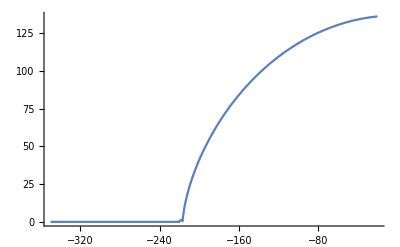

```mathematica
Plot[√(ⅇ^v1[z])/.nsolKv,{z,mid,-20},PlotRange->All]
```

```mathematica
newbdy={ K1[z1]->K1[z] , K2[z1]-> K2[z],Ex[z]->ⅇ^v1[z],Eϕ[z]->ⅇ^v2[z]}/.nsolKv/.z-> mid/.z1-> mid
```

{K1[-350]→3.75714,K2[-350]→-2.80917,Ex[-350]→0.0545453,Eϕ[-350]→3.8379×10^108}

```mathematica
bdyKu={K1[z]== K1[x0],K2[z]== K2[x0],u[z]==Log[Eϕ[x0]],Ex[z]== Ex[x0]}/.x0->mid/.newbdy/.z-> mid
```

{K1[-350]==3.75714,K2[-350]==-2.80917,u[-350]==250.024,Ex[-350]==0.0545453}

```mathematica
bdyKu1={K1[z]->  K1[x0],K2[z]->  K2[x0],Ex[z]->  Ex[x0]}/.x0->mid/.newbdy
```

{K1[z]→3.75714,K2[z]→-2.80917,Ex[z]→0.0545453}

```mathematica
asymp=eomKEuasym/.{K1'[z]->0,K2'[z]->0}/.parameters/.bdyKu1
```

{6.57252×10^-14,-1.24345×10^-14,-1.4611×10^-16+Ex'[z],1.7759+u'[z]}

```mathematica
uns=DSolve[{asymp[[4]]==0,bdyKu[[3]]},u[z],z]//Expand//Flatten
```

{u[z]→-371.539-1.7759 z}

```mathematica
nsolutionODEKu={bdyKu1,uns,K1'[z]->0,K2'[z]->0,Ex'[z]->0,Ex''[z]->0}//Flatten
```

{K1[z]→3.75714,K2[z]→-2.80917,Ex[z]→0.0545453,u[z]→-371.539-1.7759 z,K1'[z]→0,K2'[z]→0,Ex'[z]→0,Ex''[z]→0}

```mathematica
eomKEuasym/.nsolutionODEKu/.D[nsolutionODEKu, z]/.parameters
```

{6.39488×10^-14,-1.24345×10^-14,-1.4611×10^-16,0.}

## stability as z → -∞

```mathematica
chvar
```

{Kx[z]→(ⅇ^u[z] K1[z])/(√Ex[z]),Kϕ[z]→√Ex[z] K2[z],Eϕ[z]→ⅇ^u[z],Kx'[z]→-(ⅇ^u[z] K1[z] Ex'[z])/(2 Ex[z]^(3/2))+(ⅇ^u[z] K1'[z])/(√Ex[z])+(ⅇ^u[z] K1[z] u'[z])/(√Ex[z]),Kϕ'[z]→(K2[z] Ex'[z])/(2 √Ex[z])+√Ex[z] K2'[z],Eϕ'[z]→ⅇ^u[z] u'[z]}

```mathematica
nsolutionODEKu={K1[t,x]->(K1[z]/.nsolutionODEKu),K2[t,x]->(K2[z]/.nsolutionODEKu),Ex[t,x]->(Ex[z]/.nsolutionODEKu),u[t,x]->(u[z]/.nsolutionODEKu/.z-> x-t),Derivative[1,0][K1][t,x]->0,Derivative[1,0][K2][t,x]->0,Derivative[0,1][Ex][t,x]->0,Derivative[1,0][Ex][t,x]->0,Derivative[0,2][Ex][t,x]-> 0}
```

{K1[t,x]→3.75714,K2[t,x]→-2.80917,Ex[t,x]→0.0545453,u[t,x]→-371.539-1.7759 (-t+x),K1^(1,0)[t,x]→0,K2^(1,0)[t,x]→0,Ex^(0,1)[t,x]→0,Ex^(1,0)[t,x]→0,Ex^(0,2)[t,x]→0}

```mathematica
numer={k1->(K1[t,x]/.nsolutionODEKu),k2-> (K2[t,x]/.nsolutionODEKu),ex-> (Ex[t,x]/.nsolutionODEKu),a->-(u[t,x]/.nsolutionODEKu/.x->t),b-> -D[(u[t,x]/.nsolutionODEKu), x]}
```

{k1→3.75714,k2→-2.80917,ex→0.0545453,a→371.539,b→1.7759}

```mathematica
eom={Derivative[1,0][Kx][t,x],Derivative[1,0][Kϕ][t,x],Derivative[1,0][Ex][t,x],Derivative[1,0][Eϕ][t,x]}-({Derivative[1,0][Kx][t,x],Derivative[1,0][Kϕ][t,x],Derivative[1,0][Ex][t,x],Derivative[1,0][Eϕ][t,x]}/.(Solve[effeom,{Derivative[1,0][Kx][t,x],Derivative[1,0][Kϕ][t,x],Derivative[1,0][Ex][t,x],Derivative[1,0][Eϕ][t,x]}]//Flatten));
```

```mathematica
eom1=eom/.{Kx[t,x]->(ⅇ^u[t,x] K1[t,x])/(√Ex[t,x]),Kϕ[t,x]->√Ex[t,x] K2[t,x],Eϕ[t,x]->ⅇ^u[t,x]}/.D[{Kx[t,x]->(ⅇ^u[t,x] K1[t,x])/(√Ex[t,x]),Kϕ[t,x]->√Ex[t,x] K2[t,x],Eϕ[t,x]->ⅇ^u[t,x]}, t]/.D[{Kx[t,x]->(ⅇ^u[t,x] K1[t,x])/(√Ex[t,x]),Kϕ[t,x]->√Ex[t,x] K2[t,x],Eϕ[t,x]->ⅇ^u[t,x]}, x];
eom2=eom/.{Kx[t,x]->(Eϕ[t,x] K1[t,x])/(√Ex[t,x]),Kϕ[t,x]->√Ex[t,x] K2[t,x]}/.D[{Kx[t,x]->(Eϕ[t,x] K1[t,x])/(√Ex[t,x]),Kϕ[t,x]->√Ex[t,x] K2[t,x]}, t]/.D[{Kx[t,x]->(Eϕ[t,x] K1[t,x])/(√Ex[t,x]),Kϕ[t,x]->√Ex[t,x] K2[t,x]}, x];
eom1/.nsolutionODEKu/.D[nsolutionODEKu, t]/.parameters/.numer//Simplify
```

{1.25431×10^-160 ⅇ^(1.7759 t-1.7759 x),2.03971×10^-15,1.4611×10^-16,-9.74878×10^-178 ⅇ^(1.7759 t-1.7759 x)}

```mathematica
perturb2={K1[t,x]->k1(1+ϵ c1[t,x]),K2[t,x]->k2(1+ϵ c2[t,x]),Ex[t,x]->ex(1+ϵ p1[t,x]),Eϕ[t,x]->Exp[-a-b(x-t)](1+ϵ p2[t,x])};
perturb1={K1[t,x]->k1(1+ϵ c1[t,x]),K2[t,x]->k2(1+ϵ c2[t,x]),Ex[t,x]->ex(1+ϵ p1[t,x]),u[t,x]->-a-b(x-t)+ϵ p2[t,x]};
```

```mathematica
expand=(Series[(eom2//Expand)/.perturb2/.D[perturb2, t]/.D[perturb2, x]/.D[D[perturb2, x], x],{ϵ,0,1}]//Simplify)//Normal;
```

```mathematica
expand1=(Series[(eom1//Expand)/.perturb1/.D[perturb1, t]/.D[perturb1, x]/.D[D[perturb1, x], x],{ϵ,0,1}]//Simplify)//Normal;
```

```mathematica
expand-expand1//Expand//Simplify
```

{0,0,0,0}

```mathematica
firstorder=D[expand, ϵ]//Simplify;
```

```mathematica
eq1=({firstorder[[1]]/(1/(8 ex^(3/2) β^2 Δ)ⅇ^(-a+b t-b x)),firstorder[[2]]/(1/(4 √ex β^2 Δ)),firstorder[[3]]/ex,firstorder[[4]]/(1/(β √Δ)ⅇ^(-a+b t-b x))}//Simplify);
```

```mathematica
solc=Solve[{eq1[[3]]==0,eq1[[4]]==0},{c1[t,x],c2[t,x]}]//TrigReduce//Simplify//Flatten;
```

```mathematica
eq2=(Series[(eq1/.solc/.D[solc, t]/.D[solc, x])/.ⅇ^(2 (a+b (-t+x)))-> s,{s,0,0}]//Normal)/.numer/.parameters//Expand//Chop
```

{0.0873965 p1[t,x]+0.0152796 p1^(1,0)[t,x]+0.0984253 p2^(1,0)[t,x]+0.0086039 p1^(2,0)[t,x],-0.0873965 p1[t,x]-0.0492126 p1^(1,0)[t,x]+0.0180105 p2^(1,0)[t,x]+0.0101417 p2^(2,0)[t,x],0,0}

```mathematica
solp=DSolve[{eq2[[1]]==0,eq2[[2]]==0},{p1[t,x],p2[t,x]},{t,x}]//Expand//Flatten//Chop
```

{p1[t,x]→0.845318 ⅇ^(-1.7759 t) C[1][x]+0.154682 ⅇ^(-0.887948 t) Cos[8.05483 t] C[1][x]+0.203424 ⅇ^(-0.887948 t) Sin[8.05483 t] C[1][x]+0.124149 ⅇ^(-0.887948 t) Sin[8.05483 t] C[2][x]-0.174202 ⅇ^(-1.7759 t) C[4][x]+0.174202 ⅇ^(-0.887948 t) Cos[8.05483 t] C[4][x]-0.0192036 ⅇ^(-0.887948 t) Sin[8.05483 t] C[4][x],p2[t,x]→-0.291431 C[1][x]+0.422659 ⅇ^(-1.7759 t) C[1][x]-0.131228 ⅇ^(-0.887948 t) Cos[8.05483 t] C[1][x]+0.0787198 ⅇ^(-0.887948 t) Sin[8.05483 t] C[1][x]+0.0738939 C[2][x]-0.0738939 ⅇ^(-0.887948 t) Cos[8.05483 t] C[2][x]-0.00814591 ⅇ^(-0.887948 t) Sin[8.05483 t] C[2][x]+1. C[3][x]+0.0871009 C[4][x]-0.0871009 ⅇ^(-1.7759 t) C[4][x]+0.104945 ⅇ^(-0.887948 t) Sin[8.05483 t] C[4][x]}

```mathematica
u[t,x]/.nsolutionODEKu
```

-371.539-1.7759 (-t+x)

```mathematica
Limit[{p1[t,x],p2[t,x]}/.solp,t-> ∞]
```

{0.,-0.291431 C[1][x]+0.0738939 C[2][x]+1. C[3][x]+0.0871009 C[4][x]}

```mathematica
Limit[{c1[t,x],c2[t,x]}/.solc/.solp/.D[solp, t]/.D[solp, x]/.numer/.parameters//Expand,t-> ∞]//Chop
```

{0,0}